# Упражнение 8. Интерполиране с обобщени полиноми.

## 1 зад. Постройте тригонометричен полином τ(t) с период Т=2π, който интерполира таблицата: t | 0 | π/3 | (5π)/6 | (4π)/3 | (11π)/6 τ(t) | 9 | 11.1 | 14.9 | 12.9 | 9 Постройте полинома p(t) и точките на една графика в интервала [0,4π].

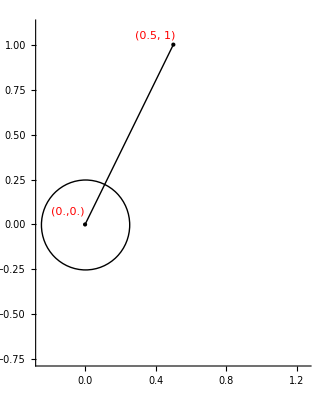
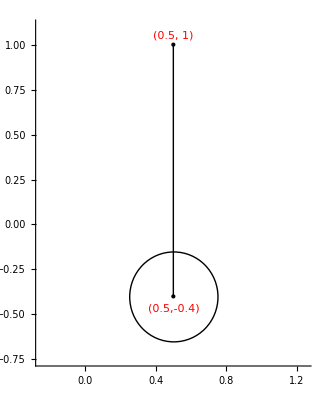
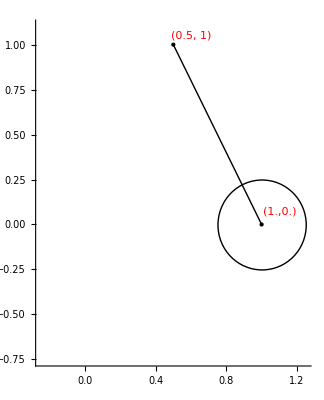
## 2 зад. Дадено е просто махало: https://learn.fmi.uni-sofia.bg/mod/resource/view.php?id=130889 Да се създаде анимация на махалото. За целта е въведена подходяща координатна система и в нея са дадени следните 5 сцени от движението на махалото: -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- "t=0" | "t=1" | "t=2" | "t=3" | "t=4" Упътване : За да анимираме махалото е достатъчно да можем да пресмятаме координатите на неговия център (x(t), y(t)), които са функции на времето. За целта ще построим 2 обобщени полинома x (t) и y (t), които интерполират данните: t | 0 | 1 | 2 | 3 | 4 x(t) | 0 | 0.5 | 1 | 0.5 | 0 y(t) | 0 | -0.4 | 0 | -0.4 | 0 Понеже данните са периодични (с период T=4), то е подходящо да търсим тригонометричен полином. Обърнете внимание, че в момента данните не са в интервала [0,2π), което означава, че не е гарантирано, че съществува единствен полином, който ги интеролира. Поради това е необходимо да се направи смяна на променливата t, принадлежаща на интервала [0,4], в променливата t_1 в интервала [0,2π).

```mathematica
Animate[Graphics[{Circle[{0,0},0.25],Line[{{0,0},{0.5,1}}]},
				PlotRange->{{-0.25,1.25},{-0.75,1.1}}, Axes->True],{t,0,2Pi,0.1},AnimationRate->5]
```

## 3 зад. Дадени са точките а) (0,1),(1,2), (2,3), ..., (10,11); Б) (0,1), (1,2), (2,3), ..., (500, 501). За всяка една от подточките да се намери обобщен полином a_0+a_1 x+a_2 x^2+....+a_n x^n, който да интерполира точките, като за целта използвате функциите в Wolfram Mathematica Sum, Table и NSolve. Сравнете получените резултати с точното решение 1+x.

## 4 зад. Напишете функция trigLagrange[nodes_,values_,x_],която да пресмята обобщен тригонометричен полином τ(x) по дадени възли nodes и стойности values, използвайки интерполационната формула на Лагранж. В нея вместо да използвате базисните полиноми на Лагранж, използвайте следния базис: τ_k(x)=(Sin[(x-x_0)/2]...Sin[(x-x_(k-1))/2]Sin[(x-x_(k+1))/2]...Sin[(x-x_n)/2])/(Sin[(x_k-x_0)/2]...Sin[(x_k-x_(k-1))/2]Sin[(x_k-x_(k+1))/2]...Sin[(x_k-x_n)/2]). Тествайте функцията върху задача 1. Сравнете получените резултати.

```mathematica
LagrangeBasis[nodes_,k_,x_]:=Product[If[k≠j,(x-nodes[[j]])/(nodes[[k]]-nodes[[j]]),1],{j,1,Length[nodes]}];
Lagrange[nodes_,values_,x_]:=Expand[Sum[ values[[i]]*LangrangeBasis[nodes,i,x],{i,1,Length[nodes]}]];
Lagrange[{0,1,2,3,4},{1,2,3,4,5},x]
```

1+x